## Szilard engine (2 states, energy version), finite-time cycle τ Problem 15.22

```mathematica
Clear["Global`*"];
```

quasistatic case, perfect observations

```mathematica
ps=ⅇ^-E0/(1+ⅇ^-E0);  Wavg=-Integrate[ps,{E0,Emax,0},Assumptions->Emax>0]
```

Emax-Log[1/2 (1+ⅇ^Emax)]

```mathematica
Winf[E_]:=Log[2/(1+Exp[-E])];
FullSimplify[Winf[Emax]/Wavg,Assumptions->Emax>0]
```

1

quasistatic case, noisy observations  P_right=1-ϵ,  P_wrong = ϵ

```mathematica
Wavg1=Wavg+ϵ Emax; dWavg1=D[Wavg1,Emax]
```

1-ⅇ^Emax/(1+ⅇ^Emax)+ϵ

```mathematica
Solve[{D[Wavg1,Emax]==0,Emax>0},Emax]
```

{{Emax→ConditionalExpression[Log[(-1-ϵ)/ϵ], -1/2<ϵ<0]}}

```mathematica
Wavg2=Wavg1/.Emax->Log[(1-ϵ)/ϵ]
```

-Log[1/2 (1+(1-ϵ)/ϵ)]+Log[(1-ϵ)/ϵ]+ϵ Log[(1-ϵ)/ϵ]

```mathematica
FullSimplify[Wavg2+Log[2]+ϵ Log[ϵ]+(1-ϵ)Log[1-ϵ],Assumptions->ϵ>0]
```

2 Log[2-2 ϵ]

Finite rate, perfect observations.  Numerical exploration

```mathematica
Wexert[E0_,τ_]:=Module[{EE,t,eqs,init,p,pars,psol,τmax,Einit},
{EE[t_]:=E0(1-t/τ);
eqs={p'[t]==ⅇ^(-EE[t])(1-p[t])-p[t]};
init=p[0]==0;
τmax=τ;
Einit=E0;
pars={E0->Einit,τ->τmax};
psol=NDSolveValue[{eqs/.pars,init},p,{t,0,τmax}];
(* pplot=LogLogPlot[{psol[t],1/2},{t,0,τmax},PlotRange->All,PlotStyle->{,Directive[Blue,Dashed,Thin]}] *)
W=NIntegrate[psol[t] EE'[t]/.pars,{t,0,τmax}]}[[1]]]
```

```mathematica
vals=Table[10^i,{i,-1,4,0.1}];   (* warning:  takes ~ 1 min. on my machine *)
Wextract1=-Map[Wexert[1,#]&,vals];
Wextract2=-Map[Wexert[2,#]&,vals];
Wextract8=-Map[Wexert[8,#]&,vals];
(* negative sign for energy extraction *)
```

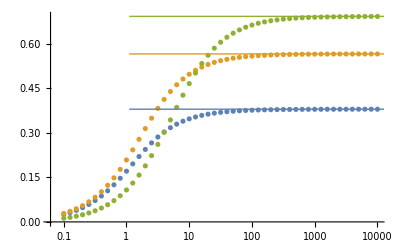

```mathematica
Show[ListLogLinearPlot[{{vals,Wextract1}ᵀ,{vals,Wextract2}ᵀ,{vals,Wextract8}ᵀ}],Plot[{Winf[1],Winf[2],Winf[8]},{x,0.1,10^4}]]
```

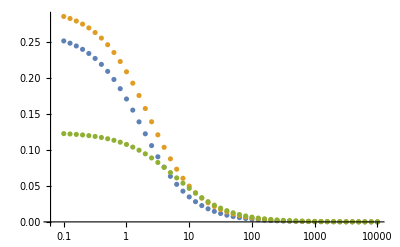

```mathematica
Pextract1=Wextract1/vals;Pextract2=Wextract2/vals; Pextract8=Wextract8/vals;
ListLogLinearPlot[{{vals,Pextract1}ᵀ,{vals,Pextract2}ᵀ,{vals,Pextract8}ᵀ}]
```

```mathematica
power=Table[-Wexert[eps,10^-6]/10^-6,{eps,0.1,10,0.1}];
```

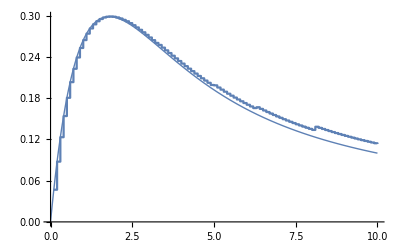

```mathematica
Show[ListPlot[power,DataRange->{0.1,10}],Plot[(1-ⅇ^-E0)/E0-ⅇ^-E0,{E0,0,10}]]
```

```mathematica
FindMaximum[(1-ⅇ^-E0)/E0-ⅇ^-E0,{E0,2}]
```

{0.298426,{E0→1.79328}}

Export data

```mathematica
dat={vals,Wextract2,Wextract8}ᵀ;
(* 
SetDirectory[NotebookDirectory[]];
Export["szilardFiniteTime.dat",dat];
*)
```

```mathematica
Wexert1[E0_,τ_]:=Module[{EE,t,eqs,init,p,pars,psol,τmax,Einit},
{EE[t_]:=E0(1-t/τ);
eqs={p'[t]==ⅇ^(-EE[t])(1-p[t])-p[t]};
init=p[0]==0;
τmax=τ;
Einit=E0;
pars={E0->Einit,τ->τmax};
psol=NDSolveValue[{eqs/.pars,init},p,{t,0,τmax}];
psol}]
```

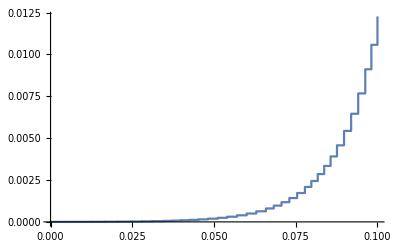

```mathematica
ListPlot[Wexert1[8,0.1]]
```